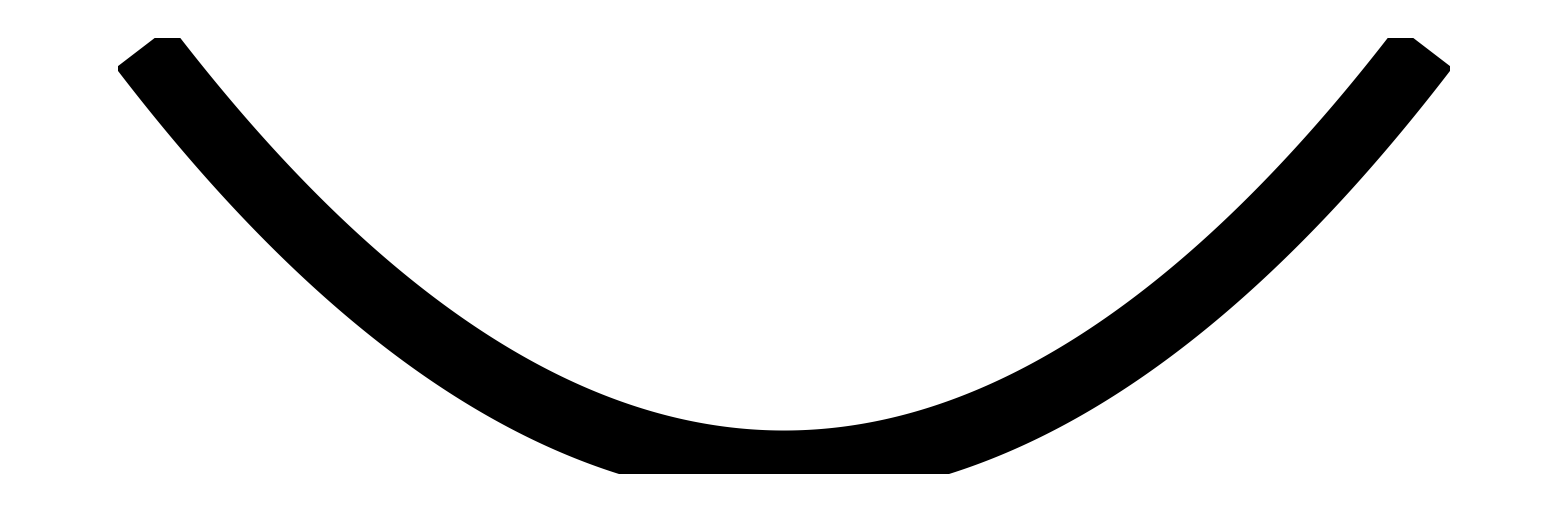

```mathematica
l1=Table[{x,0.05x^2},{x,-10,10,0.01}];
g=Graphics[{Thickness[0.05],Line[l1]},ImageSize->{2048,512},Background->None]
```

```mathematica
Export["parabolla.png",Image[g]]
```

parabolla.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["parabolla.png"]]]
```